# Relativistic Love numbers [ApJ 677 : 1216-1220]

```mathematica
Exit[]
```

```mathematica
(* This set up the working directory of the notebook. *)
path=SetDirectory[NotebookDirectory[]];
SetDirectory[path];
```

#### Colors

```mathematica
Comb1={RGBColor["#206a5d"],RGBColor["#81b214"],RGBColor["#ffcc29"],RGBColor["#f58634"]};
Comb2={RGBColor["#d92027"],RGBColor["#ff9234"],RGBColor["#ffcd3c"],RGBColor["#35d0ba"]};
Comb3={RGBColor["#252525"],RGBColor["#6930c3"],RGBColor["#64dfdf"],RGBColor["#80ffdb"]};
Comb4={RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#40a8c4"],RGBColor["#a2d5f2"]};

Comb5={RGBColor["#FBF46D"],RGBColor["#B4FE98"],RGBColor["#77E4D4"],RGBColor["#998CEB"]};
Comb6={RGBColor["#54436B"],RGBColor["#50CB93"],RGBColor["#71EFA3"],RGBColor["#ACFFAD"]};
Comb7={RGBColor["#F90716"],RGBColor["#FF5403"],RGBColor["#FFCA03"],RGBColor["#FFF323"]};
Comb8={RGBColor["#370665"],RGBColor["#35589A"],RGBColor["#F14A16"],RGBColor["#FC9918"]};
Comb9={RGBColor["#6E3CBC"],RGBColor["#7267CB"],RGBColor["#98BAE7"],RGBColor["#B8E4F0"]};
Comb10={RGBColor["#003f5c"],RGBColor["#58508d"],RGBColor["#bc5090"],RGBColor["#ff6361"]};
```

### Function for geometric quantities

```mathematica
Chr[metric_,Ig_,y_]:=Block[{ϵ,𝒶0,l1,l2,l3,l4,dim = Length[y],Christoffel},

Christoffel = Table[Sum[Ig[[l1,l4]]D[metric[[l2,l4]],y[[l3]]],{l4,1,dim}],{l1,1,dim},{l2,1,dim},{l3,1,dim}]
+Table[Sum[Ig[[l1,l4]]D[metric[[l4,l3]],y[[l2]]],{l4,1,dim}],{l1,1,dim},{l2,1,dim},{l3,1,dim}]
-Table[Sum[Ig[[l1,l4]]D[metric[[l2,l3]],y[[l4]]],{l4,1,dim}],{l1,1,dim},{l2,1,dim},{l3,1,dim}];

	Return[Collect[Series[Christoffel/2,{ϵ,0,1}],ϵ,Simplify]];

]
```

```mathematica
Riemann[metric_,y_,Christoffel_]:=Block[{ϵ,l1,l2,l3,l4,l5,dim = Length[y],Riem},
		
	Riem = Table[D[Christoffel[[l1]][[l2,l4]],y[[l3]]],{l1,1,dim},{l2,1,dim},{l3,1,dim},{l4,1,dim}]
			-Table[D[Christoffel[[l1]][[l2,l3]],y[[l4]]],{l1,1,dim},{l2,1,dim},{l3,1,dim},{l4,1,dim}]
			-Table[Sum[Christoffel[[l1]][[l5,l4]]Christoffel[[l5]][[l2,l3]],{l5,1,dim}],{l1,1,dim},{l2,1,dim},{l3,1,dim},{l4,1,dim}]
			+Table[Sum[Christoffel[[l1]][[l5,l3]]Christoffel[[l5]][[l2,l4]],{l5,1,dim}],{l1,1,dim},{l2,1,dim},{l3,1,dim},{l4,1,dim}]; 

	Return[Collect[Series[Riem,{ϵ,0,1}],ϵ,Simplify]];

]
```

```mathematica
Ricci[Riem_]:=Block[{l1,l2,l3,dim = Dimensions[Riem][[1]],RicciTensor},

RicciTensor = Table[Sum[Riem[[l3,l1,l3,l2]],{l3,dim}],{l1,dim},{l2,dim}];

Return[Collect[Series[RicciTensor,{ϵ,0,1}],ϵ,Simplify]];

]
```

```mathematica
RicciScalar[Ig_,RicciTensor_]:=Block[{l1,l2,dim = Dimensions[RicciTensor][[1]],RicciScal},

RicciScal = Sum[Ig[[l1,l2]]RicciTensor[[l1,l2]],{l1,1,dim},{l2,1,dim}];

Return[Collect[Series[RicciScal,{ϵ,0,1}],ϵ,Simplify]];

]
```

### Metric tensor

```mathematica
(* I define the metric here. This just corresponds to time independent polar perturbations *)
```

```mathematica
g0={{-A[r],0,0,0},{0,1/B[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};

h={{A[r]H0[r],H1[r],0,0},{H1[r],H2[r]/B[r],0,0},{0,0,r^2 K[r],0},{0,0,0,r^2 Sin[θ]^2 K[r]}}Y[θ,ϕ];

(* ϵ is the usual bookkeping parameter for the perturbation *)
ℊ=g0+ϵ h;

ℊℐ=Normal[Series[Inverse[ℊ],{ϵ,0,1}]];

dg=Series[-Det[g],{ϵ,0,1}];

y={t,r,θ,ϕ};
```

```mathematica
ℊ//MatrixForm
```

(-A[r]+ϵ A[r] H0[r] Y[θ,ϕ] | ϵ H1[r] Y[θ,ϕ] | 0 | 0
ϵ H1[r] Y[θ,ϕ] | 1/B[r]+(ϵ H2[r] Y[θ,ϕ])/B[r] | 0 | 0
0 | 0 | r^2+r^2 ϵ K[r] Y[θ,ϕ] | 0
0 | 0 | 0 | r^2 Sin[θ]^2+r^2 ϵ K[r] Sin[θ]^2 Y[θ,ϕ])

```mathematica
(* Christoffel symbols *)
Γ=Normal[Series[Chr[ℊ,ℊℐ,y],{ϵ,0,1}]];
```

```mathematica
(* Riemann tensor *)
Riem=Normal[Series[Riemann[ℊ,y,Γ],{ϵ,0,1}]];
```

```mathematica
(* Ricci tensor *)
Rmunu=Normal[Series[Ricci[Riem],{ϵ,0,1}]];
```

```mathematica
(* Ricci scalar *)
ℛ=Normal[Series[RicciScalar[ℊℐ,Rmunu],{ϵ,0,1}]];
```

### Field equations and stress-energy tensor

```mathematica
G=Normal[Series[Rmunu-1/2ℊ ℛ,{ϵ,0,1}]];
```

```mathematica
(* Mixed compoenent of the Einstein tensor *)
𝒢=Normal[Series[Table[Sum[ℊℐ[[l1,l3]]G[[l3,l2]],{l3,1,4}],{l1,1,4},{l2,1,4}],{ϵ,0,1}]];
```

```mathematica
(* Define the 4-velocity of the fluid and compute the stress-energy tensor *)
u={u0,0,0,0};
```

```mathematica
u0=Normal[Series[Solve[Sum[ℊℐ[[l1,l2]]u[[l1]]u[[l2]],{l1,1,4},{l2,1,4}]==-1,u0][[2,1,2]],{ϵ,0,1}]];
```

```mathematica
T=Collect[8π Series[(ρ[r]+p[r]+ϵ dpdρ^-1 δp[r]Y[θ,ϕ]+ϵ δp[r]Y[θ,ϕ])u⊗u+ℊ (p[r]+ϵ δp[r]Y[θ,ϕ]),{ϵ,0,1}],ϵ,FullSimplify];
```

```mathematica
(* Again this is the mixed compoent form *)
𝒯=Normal[Series[Table[Sum[ℊℐ[[l1,l3]]T[[l3,l2]],{l3,1,4}],{l1,1,4},{l2,1,4}],{ϵ,0,1}]];
```

```mathematica
(* Covariant derivative of the stress enegy tensor *)
𝒟T=Collect[Table[Sum[ℊℐ[[i,j]]D[T[[i,s]],y[[j]]],{j,1,4},{i,1,4}]-Series[Sum[ℊℐ[[i,j]]Γ[[β]][[j,i]]T[[β,s]],{β,1,4},{i,1,4},{j,1,4}]+Sum[ℊℐ[[i,j]]Γ[[β]][[s,j]]T[[i,β]],{β,1,4},{i,1,4},{j,1,4}],{ϵ,0,1}],{s,1,4}],ϵ,FullSimplify];
```

```mathematica
(* Export everything *)
```

```mathematica
Export["stressenergy.m",𝒯];
```

```mathematica
Export["EoMcontinuity.m",𝒟T];
```

```mathematica
Export["eq_metric.m",𝒢];
```

## Solve field’s equation order by order

```mathematica
𝒯=Import["stressenergy.m"];
𝒢=Import["eq_metric.m"];
𝒟T=Import["EoMcontinuity.m"];
```

```mathematica
(* Einstein's equations *)
ℰ=𝒢-𝒯;
```

### ϵ = 0 - Background solution. This gives you the usual TOV equations

```mathematica
Coefficient[ℰ[[1,1]],ϵ,0];
dB=Solve[%==0,B'[r]][[1,1,2]]
```

(1-B[r]-8 π r^2 ρ[r])/r

```mathematica
Coefficient[ℰ[[2,2]],ϵ,0];
dA=Solve[%==0,A'[r]][[1,1,2]]
```

-(A[r] (-1+B[r]-8 π r^2 p[r]))/(r B[r])

```mathematica
Coefficient[𝒟T[[2]],ϵ,0];
dp=Solve[%==0,p'[r]][[1,1,2]]
```

-((p[r]+ρ[r]) A'[r])/(2 A[r])

```mathematica
dM=Solve[D[1-(2M[r])/r,r]==(dB//.{B[r]->1-(2M[r])/r}),M'[r]][[1,1,2]]
```

4 π r^2 ρ[r]

```mathematica
dp2=dp//.{A'[r]->dA,B[r]->1-(2M[r])/r}//Simplify
```

-((M[r]+4 π r^3 p[r]) (p[r]+ρ[r]))/(r (r-2 M[r]))

```mathematica
(* Check for the vacuum case: it must reproduce Schwarzschild *)
```

```mathematica
dB//.ρ[r]->0;
BS=DSolve[%==B'[r],B[r],r][[1,1,2]]//.C[1]->-2M
```

1-(2 M)/r

```mathematica
dA//.{p[r]->0,B[r]->BS};
As=DSolve[%==A'[r],A[r],r][[1,1,2]]//.C[1]->1//Simplify
```

1-(2 M)/r

### ϵ = 1 - Fist order equations in the quadrupolar perturbation

```mathematica
(* From this equation I find H0+H2 = 0 *)
Simplify[Coefficient[ℰ[[3,3]]-ℰ[[4,4]],ϵ,1]]
```

-((H0[r]-H2[r]) (Csc[θ]^2 Y^(0,2)[θ,ϕ]+Cot[θ] Y^(1,0)[θ,ϕ]-Y^(2,0)[θ,ϕ]))/(2 r^2)

```mathematica
(* I impose the previous condition *)
H0[r_]:=H[r];
H2[r_]:=H[r];
```

```mathematica
(* Find the solution for K *)
Coefficient[ℰ[[2,3]],ϵ,1]//Simplify;
dK=Solve[%==0,K'[r]][[1,1,2]]
```

(H[r] A'[r]+A[r] H'[r])/A[r]

```mathematica
(* Find the solution for δp *)
Coefficient[ℰ[[3,3]]+ℰ[[4,4]],ϵ,1]//.{K'[r]->dK,K''[r]->D[dK,r]}//Simplify;
solδp=Solve[%==0,δp[r]][[1,1,2]]
```

(H[r] (B[r] A'[r]-A[r] B'[r]))/(16 π r A[r])

```mathematica
(* Simplify the master equation for H[r] *)
Assuming[Csc[θ]^2 Derivative[0,2][Y][θ,ϕ]+Cot[θ] Derivative[1,0][Y][θ,ϕ]+Derivative[2,0][Y][θ,ϕ]==-6 Y[θ,ϕ],Simplify[Coefficient[ℰ[[1,1]]-ℰ[[2,2]],ϵ,1]//.{K'[r]->dK,K''[r]->D[dK,r],δp[r]->solδp}]];

Eq=Collect[%/(Y[θ,ϕ]B[r])//.{B'[r]->dB,A'[r]->dA,A''[r]->D[dA,r],p'[r]->dp},{H''[r],H'[r],H[r],r,dpdρ},FullSimplify]
```

H[r] (-(1+B[r] (4+B[r]))/(r^2 B[r]^2)-(64 π^2 r^2 p[r]^2)/B[r]^2+(4 π (p[r]+ρ[r]))/(dpdρ B[r])+(4 π ((-4+13 B[r]) p[r]+5 B[r] ρ[r]))/B[r]^2)+((1+1/B[r])/r+(4 π r (p[r]-ρ[r]))/B[r]) H'[r]+H''[r]

```mathematica
Coefficient[Eq,H'[r]]
```

(1+1/B[r])/r+(4 π r (p[r]-ρ[r]))/B[r]

```mathematica
(1+1/B[r])/r//.B[r]->1-(2m[r])/r//Simplify
```

1/r+1/(r-2 m[r])

```mathematica
2/r+1/B[r] 2 m[r]/r^2//.B[r]->1-(2m[r])/r//FullSimplify
```

1/r+1/(r-2 m[r])

#### Matching the solution with the exterior

```mathematica
(* We need now to find the form of the equation in vacuum to make the match between the interior and exterior solution *) 
EqR=Collect[Eq//.{p[r]->0,ρ[r]->0,A[r]->1-(2M)/r,B[r]->1-(2M)/r},{H[r],H'[r],H''[r]},FullSimplify]
```

-(2 (2 M^2-6 M r+3 r^2) H[r])/(r^2 (-2 M+r)^2)+(1/r+1/(-2 M+r)) H'[r]+H''[r]

```mathematica
(* We change the radial variable to r = M(1+x) *) 
Coefficient[EqR,H[r]]H[x]+Coefficient[EqR,H'[r]] H'[x]/M+Coefficient[EqR,H''[r]] H''[x]/M^2//.r->M(1+x);
HR2[x_]=Collect[%(-1+x^2)M^2,{H[x],H'[x],H''[x]},FullSimplify]
```

((2-6 x^2) H[x])/(-1+x^2)+2 x H'[x]+(-1+x^2) H''[x]

```mathematica
(* Back again to r *) 
solHR=Collect[DSolve[HR2[z]==0,H[z],z][[1,1,2]]//.{Log[1-z]->Log[z-1],z->r/M-1},{C[1],C[2]},Simplify]
```

(3 (2 M-r) r C[1])/M^2+(C[2] (-2 M (2 M^3+4 M^2 r-9 M r^2+3 r^3)+3 r^2 (-2 M+r)^2 Log[r/M]-3 r^2 (-2 M+r)^2 Log[-2+r/M]))/(2 M^2 (2 M-r) r)

```mathematica
gttACMC=-1+(2M)/r+(3𝒬)/r^3+ℰT r^2
```

-1+(2 M)/r+r^2 ℰT+(3 𝒬)/r^3

```mathematica
(* I match the solution at infinity with ACMC coordinates to extract the quadrupole *) 
c1=Solve[Coefficient[gttACMC,r,2]==Coefficient[Series[(-1+(2M)/r)(1+solHR),{r,∞,3}],r,2],C[1]][[1,1,2]]
```

(M^2 ℰT)/3

```mathematica
c2=Solve[Coefficient[gttACMC,r,-3]==Coefficient[Series[(-1+(2M)/r)(1+solHR),{r,∞,3}],r,-3],C[2]][[1,1,2]]
```

(15 𝒬)/(8 M^3)

```mathematica
(* Finally I introduce the euqation for (𝒬 = λ ℰ) and I solve for λ *) 

Eq1=Collect[solHR//.{r->R,C[1]->c1,C[2]->c2,𝒬->λ ℰT},λ,FullSimplify];

Eq2=Collect[D[solHR,r]//.{r->R,C[1]->c1,C[2]->c2,𝒬->λ ℰT},λ,FullSimplify];
```

```mathematica
Eq1
```

(2 M-R) R ℰT+(15 ℰT λ (-2 M (M-R) (2 M^2+6 M R-3 R^2)+3 R^2 (-2 M+R)^2 (Log[R/M]-Log[-2+R/M])))/(16 M^5 (2 M-R) R)

```mathematica
Eq2
```

2 (M-R) ℰT+(15 ℰT λ (6 M+M^3 (1/R^2+1/(-2 M+R)^2)+3 (M-R) (Log[R/M]-Log[-2+R/M])))/(8 M^5)

```mathematica
(* HR = H(R), DHR = H'(R)*)
Solve[{Eq1==HR,Eq2==DHR},{ℰT,λ}][[1,2,2]]//.{M->R 𝒞,DHR->(HR 𝓎)/R}//FullSimplify
```

(16 R^5 (1-2 𝒞)^2 𝒞^5 (2+2 𝒞 (-1+𝓎)-𝓎))/(15 (2 𝒞 (6-3 𝓎+𝒞 (3 (-8+5 𝓎)+2 𝒞 (13-11 𝓎+𝒞 (-2+3 𝓎+2 𝒞 (1+𝓎)))))+3 (1-2 𝒞)^2 (2+2 𝒞 (-1+𝓎)-𝓎) Log[-2+1/𝒞]-3 (1-2 𝒞)^2 (2+2 𝒞 (-1+𝓎)-𝓎) Log[1/𝒞]))

```mathematica
(* k2 is defined in terms of the compactness C=M/R and of the varibale 𝓎 = R H'[R]/H[r], i.e. a combination of H and its derivative at the stellar surface *)
k2=Assuming[𝒞<=1/2,FullSimplify[3/2/R^5Solve[{Eq1==HR,Eq2==DHR},{ℰT,λ}][[1,2,2]]//.{M->R 𝒞,DHR->(HR 𝓎)/R}]]
```

(8 (1-2 𝒞)^2 𝒞^5 (2+2 𝒞 (-1+𝓎)-𝓎))/(10 𝒞 (6-3 𝓎+𝒞 (3 (-8+5 𝓎)+2 𝒞 (13-11 𝓎+𝒞 (-2+3 𝓎+2 𝒞 (1+𝓎)))))+15 (1-2 𝒞)^2 (2+2 𝒞 (-1+𝓎)-𝓎) Log[1-2 𝒞])

```mathematica
aa=8/5𝒞^5*(1-2*𝒞)^2*(2+2𝒞*(w-1)-w)/(2𝒞*(6-3w + 
		3𝒞*(5w-8))+4𝒞^3*(13-11w+𝒞*(3w-2)+2𝒞^2 * 
		(1+w))+3(1-2𝒞)^2*(2-w+2𝒞*(w-1))*Log[1-2𝒞])//.w->𝓎
```

(8 (1-2 𝒞)^2 𝒞^5 (2+2 𝒞 (-1+𝓎)-𝓎))/(5 (4 𝒞^3 (13-11 𝓎+2 𝒞^2 (1+𝓎)+𝒞 (-2+3 𝓎))+2 𝒞 (6-3 𝓎+3 𝒞 (-8+5 𝓎))+3 (1-2 𝒞)^2 (2+2 𝒞 (-1+𝓎)-𝓎) Log[1-2 𝒞]))

```mathematica
k2/aa//Simplify
```

1

```mathematica
k2//.{𝒞->0.2,𝓎->-1}
```

0.177984

## Numerical integration

```mathematica
<<stellar`
```

```mathematica
apr=Import["./eos_tabulated/apr.dat"]; (* soft *)
gnh3=Import["./eos_tabulated/gnh3.dat"]; (* stiff *)
sly4=Import["./eos_tabulated/sly4.dat"];
```

```mathematica
tov[apr,1.235 10.^-4,"F",100,2];
```

| M[M_⊙] | R[km] | 𝒞 | k_2 | λ[km^5]
 | 1.39938 | 11.3333 | 0.182349 | 0.0750756 | 9358.13

```mathematica
tov[apr,1.235 10.^-4,"T",200,2]
```

| M[M_⊙] | R[km] | 𝒞 | k_2 | λ[km^5]
 | 1.62436 | 13.5261 | 0.177351 | 0.0592202 | 17874.5

{1.62436,13.5261,0.177351,0.0592202,17874.5}

```mathematica
prange=Range[-5,-2.5,0.05];
```

```mathematica
dataAPR=Monitor[Table[tov[apr,10^prange[[i]],"F",100,2],{i,1,Length[prange]}],i];
```

```mathematica
datagnh3=Monitor[Table[tov[gnh3,10^prange[[i]],"F",100,2],{i,1,Length[prange]}],i];
```

```mathematica
datasly=Monitor[Table[tov[sly4,10^prange[[i]],"F",100,2],{i,1,Length[prange]}],i];
```

```mathematica
datapoly=Monitor[Table[tov[sly4,10^prange[[i]],"T",100,2],{i,1,Length[prange]}],i];
```

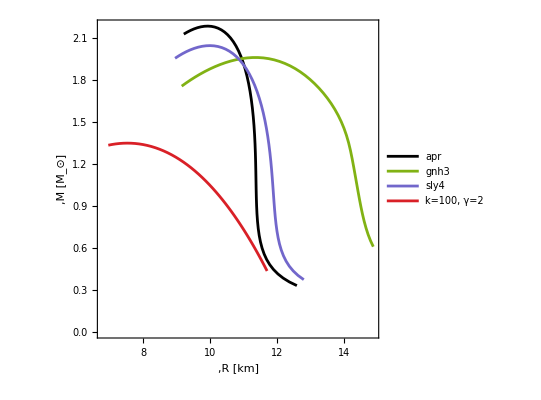

```mathematica
ListPlot[{dataAPR[[All,{2,1}]],datagnh3[[All,{2,1}]],datasly[[All,{2,1}]],datapoly[[All,{2,1}]]},Joined->True,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,ImageSize->400,FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],FrameLabel->{{Style[",M [M_⊙]",18],None},{Style[",R [km]",18],None}},PlotStyle->{Directive[Black,AbsoluteThickness[2]],Directive[Comb1[[2]],AbsoluteThickness[2]],Directive[Comb9[[2]],AbsoluteThickness[2]],Directive[Comb2[[1]],AbsoluteThickness[2]]},ImagePadding->{{85,15}, {65, 10}},PlotLegends->Placed[{Style["apr",14,FontFamily->"Palatino"],Style["gnh3",14,FontFamily->"Palatino"],Style["sly4",14,FontFamily->"Palatino"],Style["k=100, γ=2",14,FontFamily->"Palatino"]},Scaled[{0.23,0.18}]]]
```

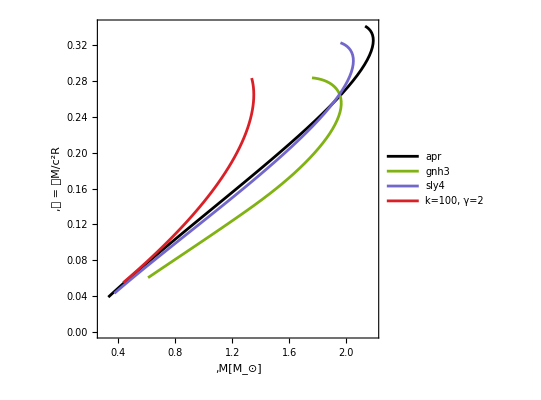

```mathematica
ListPlot[{dataAPR[[All,{1,3}]],datagnh3[[All,{1,3}]],datasly[[All,{1,3}]],datapoly[[All,{1,3}]]},Joined->True,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,ImageSize->400,FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],FrameLabel->{{Style[",𝒞 = 𝒢M/c^2R",18],None},{Style[",M[M_⊙]",18],None}},PlotStyle->{Directive[Black,AbsoluteThickness[2]],Directive[Comb1[[2]],AbsoluteThickness[2]],Directive[Comb9[[2]],AbsoluteThickness[2]],Directive[Comb2[[1]],AbsoluteThickness[2]]},ImagePadding->{{85,15}, {65, 10}},PlotLegends->Placed[{Style["apr",14,FontFamily->"Palatino"],Style["gnh3",14,FontFamily->"Palatino"],Style["sly4",14,FontFamily->"Palatino"],Style["k=100, γ=2",14,FontFamily->"Palatino"]},Scaled[{0.2,0.8}]]]
```

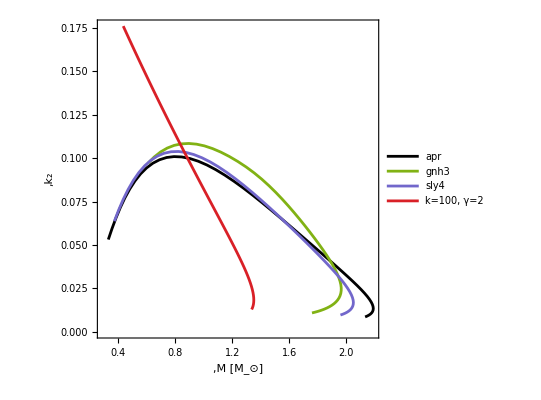

```mathematica
ListPlot[{dataAPR[[All,{1,4}]],datagnh3[[All,{1,4}]],datasly[[All,{1,4}]],datapoly[[All,{1,4}]]},Joined->True,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,ImageSize->400,FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],FrameLabel->{{Style[",k_2",20],None},{Style[",M [M_⊙]",18],None}},PlotStyle->{Directive[Black,AbsoluteThickness[2]],Directive[Comb1[[2]],AbsoluteThickness[2]],Directive[Comb9[[2]],AbsoluteThickness[2]],Directive[Comb2[[1]],AbsoluteThickness[2]]},ImagePadding->{{85,15}, {65, 10}},PlotLegends->Placed[{Style["apr",14,FontFamily->"Palatino"],Style["gnh3",14,FontFamily->"Palatino"],Style["sly4",14,FontFamily->"Palatino"],Style["k=100, γ=2",14,FontFamily->"Palatino"]},Scaled[{0.8,0.8}]]]
```

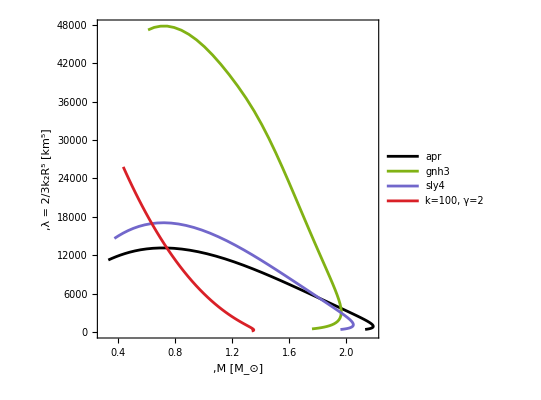

```mathematica
ListPlot[{dataAPR[[All,{1,5}]],datagnh3[[All,{1,5}]],datasly[[All,{1,5}]],datapoly[[All,{1,5}]]},Joined->True,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,ImageSize->400,FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],FrameLabel->{{Style[",λ = 2/3k_2R^5 [km^5]",18],None},{Style[",M [M_⊙]",18],None}},PlotStyle->{Directive[Black,AbsoluteThickness[2]],Directive[Comb1[[2]],AbsoluteThickness[2]],Directive[Comb9[[2]],AbsoluteThickness[2]],Directive[Comb2[[1]],AbsoluteThickness[2]]},ImagePadding->{{85,15}, {65, 10}},PlotLegends->Placed[{Style["apr",14,FontFamily->"Palatino"],Style["gnh3",14,FontFamily->"Palatino"],Style["sly4",14,FontFamily->"Palatino"],Style["k=100, γ=2",14,FontFamily->"Palatino"]}
,Scaled[{0.8,0.8}]]]
```